```mathematica
alpha1 = (1/0.45)^2;
dist = GammaDistribution[alpha1, 18/alpha1]
lst = {}
```

GammaDistribution[4.93827,3.645]

{}

```mathematica
For[i=0,i<=200,i++,AppendTo[lst,PDF[ dist, i]]]
For[i=1,i<=201,i++,lst[[i]] = Round[lst[[i]], 0.000001]]
```

```mathematica
Export["/Users/Jake/Desktop/Current Classes/CS 156b/firewall-covid/Imperial College Model/AdjustedPi.csv",lst,"csv"];
```

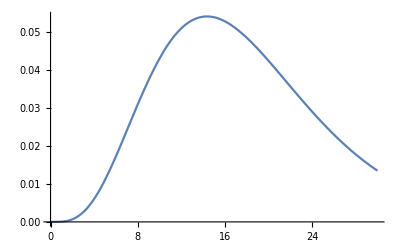

```mathematica
Plot[PDF[dist, x], {x, 0, 30}]
```

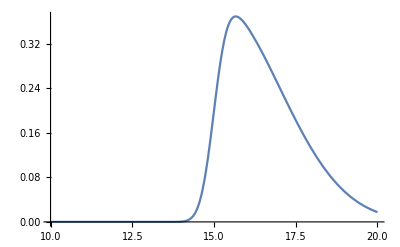

```mathematica
dist = SkewNormalDistribution[15, 2, 6], x], {x, 10, 20}
```

```mathematica
For[i=0,i<=200,i++,AppendTo[lst,PDF[ dist, i]]]
For[i=1,i<=201,i++,lst[[i]] = Round[lst[[i]], 0.000001]]
```

```mathematica
Export["/Users/Jake/Desktop/Current Classes/CS 156b/firewall-covid/Imperial College Model/AdjustedPi.csv",lst,"csv"];
```